```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ujwalkumar/Desktop/Classes/Semester 8/Computational Physics/Homework 9

```mathematica
data=ReadList["!./metropolis 100000",Number];
```

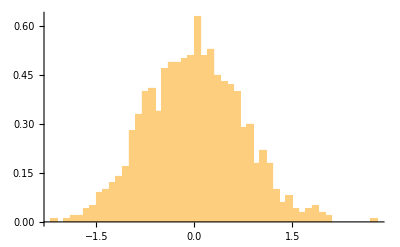

```mathematica
Show[Histogram[data[[;;;;100]],100,"PDF"],Plot[p[x]/n,{x,-5,15},PlotRange->All]]
```

```mathematica
p[x_]:=Exp[-x^2]+2Exp[-(x-5)^2/.5];
n=NIntegrate[p[x],{x,-Infinity,Infinity}];
```

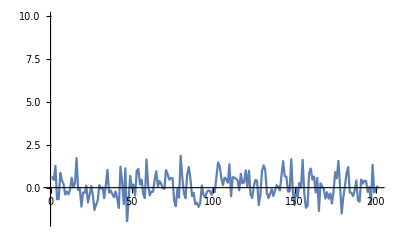

```mathematica
ListLinePlot[data[[100;;4100;;20]],PlotRange->{-2,10}]
```

```mathematica
dataind=RandomVariate[NormalDistribution[0,1/√2],200];
```

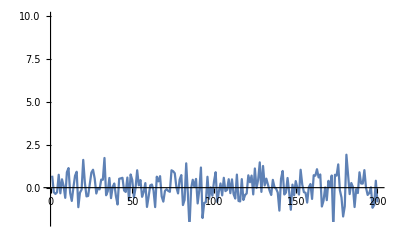

```mathematica
ListLinePlot[dataind,PlotRange->{-2,10}]
```

```mathematica
data=ReadList["!./gas 200 40 0.5 0.1 0.1 10 10",Number];
```

```mathematica
display[l_,n_,sz_]:=Graphics[{{FaceForm[],EdgeForm[Black],Rectangle[{0,0},{sz,sz}]},AbsolutePointSize[6],Table[Point[{l[[2+4*i]],l[[3+4*i]]}],{i,0,n-1}]},PlotRange->{{-0.2,sz+0.2},{-0.2,sz+0.2}}]
```